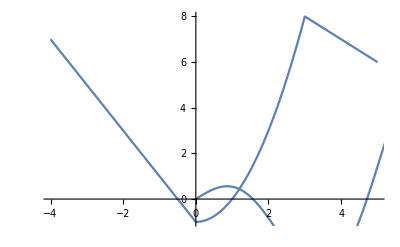

```mathematica
u[x_]:=-2x-1/;x≤0
u[x_]:=x^2-1/;0<x≤3
u[x_]:=11-x/;x>3
v[x_]:=x*Cos[x]
m=Plot[u[x],{x,-4,5},DisplayFunction->Identity];
n=Plot[v[x],{x,0,9},DisplayFunction->Identity];
Show[m,n,DisplayFunction->$DisplayFunction]
```